```mathematica
1.NALOGA
```

```mathematica
Simplify[(x^5-2x^2+3x+4)/(x^5 - 2x -1)]/.x->{1,2,3,4}
```

```mathematica
{-3,34/27,119/118,144/145}
f[x_]:=(x^5-2x^2+3x+4)/(x^5 - 2x -1)
```

{-3,34/27,119/118,144/145}

```mathematica
f[1]
```

-3

```mathematica
Table[(x^5-2x^2+3x+4)/(x^5 - 2x -1),{x,1,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
2. NALOGA
```

```mathematica
sez={10,20,30,40,50,60,70}
```

{10,20,30,40,50,60,70}

```mathematica
Take[sez,3]
```

{10,20,30}

```mathematica
Take[sez,-2 ]
```

{60,70}

```mathematica
Take[sez,{2,4}]
```

{20,30,40}

```mathematica
sez[[{2,3,5}]]
```

{20,30,50}

```mathematica
Drop[sez,{4,5}]
```

{10,20,30,60,70}

```mathematica
3. NALOGA
```

```mathematica
ClearAll[sez]
```

```mathematica
sez1={x^6,x^2,a}
```

{x^6,x^2,a}

```mathematica
ReplaceAll[sez1,x->3]
```

{{729,9,a}}

```mathematica
ReplaceAll[sez1,x->x^2]
```

{x^12,x^4,a}

```mathematica
ReplaceAll[sez1,x^2->x]
```

{x^6,x,a}

```mathematica
ReplaceAll[sez1,x->{1,2,3}]
```

{{1,64,729},{1,4,9},a}

```mathematica
ReplaceAll[sez1,{x->3,a->x}]
```

{729,9,x}

```mathematica
sez1//.{x->3,a->x}
```

```mathematica
{729,9,3}
```

{729,9,3}

```mathematica
seznov= ReplaceAll[sez1,{x->1}{x->2}{x->3}]
```

ReplaceAll::reps: {(x→1) (x→2) (x→3)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x^6,x^2,a}/.{(x→1) (x→2) (x→3)}

```mathematica
seznov
```

{x^6,x^2,a}/.{(x→1) (x→2) (x→3)}

```mathematica
4.NALOGA
```

```mathematica
ClearAll[x]
f[x_]:=x^5+4x^3-9
D[f[x],x]
```

12 x^2+5 x^4

```mathematica
D[f[x],x]/.x->{1,5}
```

{17,3425}

```mathematica
g[x_]:=ⅇ^(x^(1/4))
D[g[x],x]
```

(ⅇ^(x^(1/4)))/(4 x^(3/4))

```mathematica
D[g[x],x]/.x->{1,2}
```

{ⅇ/4,(ⅇ^(2^(1/4)))/(4 2^(3/4))}

```mathematica
FullSimplify[D[Abs[x+1],x],x∈ Reals]
```

```mathematica
Sign[1+x]
```

```mathematica
Sign[1+x]
D[Abs[x+1],x]/.x->{-1,1}
```

Sign[1+x]

Abs'[{0,2}]

```mathematica
h[x_]:=ax^2+3b
D[h[x],b]
```

3

```mathematica
5.NALOGA
```

```mathematica
ClearAll[f,g,t,n,x]
```

```mathematica
f[x_]:=x^3Log[4x+5]
```

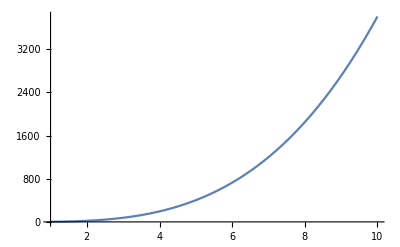

```mathematica
Plot[f[x],{x,1,10}]
```

```mathematica
f[5]
```

125 Log[25]

```mathematica
x0=5
```

5

```mathematica
k0=D[f[x],x]/.x->x0
```

20+75 Log[25]

```mathematica
n0=n/.First[Solve[f[x0]==k0*x0+n,n]]
```

n

```mathematica
t[x_]:=k0*x+n0
Plot[f[x],t[x],{x,1,10}]
```

Plot::nonopt: Options expected (instead of {x,1,10}) beyond position 2 in Plot[f[x],t[x],{x,1,10}]. An option must be a rule or a list of rules.

Plot[f[x],t[x],{x,1,10}]

```mathematica
6. NALOGA
```

```mathematica
Limit[(x^3-4x^2+2x+4)/(x^5-9x-14),x->2]
```

-2/71

```mathematica
Limit[(ArcTan[7x])/ArcSin[8x],x->0]
```

7/8

```mathematica
Limit[(x^2-25)Cot[Pi x],x->5]
```

10/π

```mathematica
Limit[(1+Cos [x])/(2*Sqrt[Pi * x]-Pi -x),x->Pi]
```

-2 π

```mathematica
Limit[Abs[x]Cot[x],x->0,Direction->+1]
```

-1

```mathematica
Limit[Abs[x]Cot[x],x->0,Direction->-1]
```

1